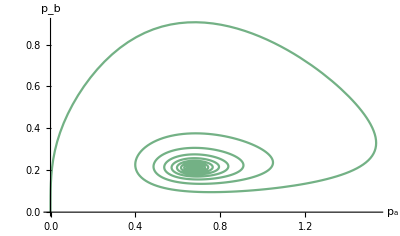

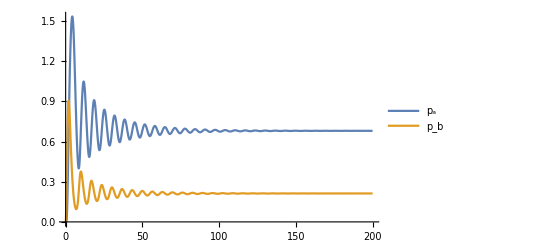

```mathematica
SuperPlus[h][p_, θ_, n_] := p^n/(p^n + θ^n)
SuperMinus[h][p_, θ_, n_] := 1-SuperPlus[h][p, θ, n]

tmax=200;

With[{ma=2., mb=2.,
	na=2.4, nb=2.4,
	θa=0.28, θb=0.28,
	 ka=1., kb=1.,
	γa=1., γb=1.,
	δa=1., δb=1.},
		sol=NDSolve[{Subscript[r, a]'[t]==ma*SuperPlus[h][Subscript[p, b][t], θb, nb]-γa*Subscript[r, a][t],
					Subscript[r, b]'[t]==mb*SuperMinus[h][Subscript[p, a][t], θa, na]-γb*Subscript[r, b][t],
					Subscript[p, a]'[t]==ka*Subscript[r, a][t]-δa*Subscript[p, a][t],
					Subscript[p, b]'[t]==kb*Subscript[r, b][t]-δb*Subscript[p, b][t],
					Subscript[r, a][0]==0,Subscript[r, b][0]==0, Subscript[p, a][0]==0.0, Subscript[p, b][0]==0.0},
					{Subscript[r, a],Subscript[r, b],Subscript[p, a], Subscript[p, b]},{t, 0, tmax}]];


ParametricPlot[Evaluate[{Subscript[p, a][t],Subscript[p, b][t]}/.First[sol]],{t,0,tmax}, AxesLabel->{Subscript[p, a],Subscript[p, b]},ColorFunction->"Rainbow", PlotRange->Full]

Plot[Evaluate[{Subscript[p, a][t],Subscript[p, b][t]}/.First[sol]],{t,0,tmax}, PlotLegends->{"p_a", "p_b"}]

Animate[ParametricPlot[Evaluate[{Subscript[p, a][t],Subscript[p, b][t]}/.First[NDSolve[{Subscript[r, a]'[t]==ma*SuperPlus[h][Subscript[p, b][t], θb, nb]-γa*Subscript[r, a][t],
					Subscript[r, b]'[t]==mb*SuperMinus[h][Subscript[p, a][t], θa, na]-γb*Subscript[r, b][t],
					Subscript[p, a]'[t]==ka*Subscript[r, a][t]-δa*Subscript[p, a][t],
					Subscript[p, b]'[t]==kb*Subscript[r, b][t]-δb*Subscript[p, b][t],
					Subscript[r, a][0]==0,Subscript[r, b][0]==0, Subscript[p, a][0]==0.0, Subscript[p, b][0]==0.0},
					{Subscript[r, a],Subscript[r, b],Subscript[p, a], Subscript[p, b]},{t, 0, tmax}]]],{t,0,tmax}, AxesLabel->{Subscript[p, a],Subscript[p, b]},ColorFunction->"Rainbow", PlotRange->Full],{ma, 1., 10.}, {mb, 1., 10.},{na, 2., 5.},{nb, 2., 5.},
{θa, 0.2, 1.}, {θb, 0.2, 1.},{ka, 1., 5.},{kb, 1., 5.},
{γa, 1., 5.}, {γb, 1., 5.}, {δa, 1., 5.}, {δb, 1., 5.},AnimationRunning->False]
```